-Graphics-

## Lesson 28: Systems of linear algebraic equations

-Graphics-

## Overview

A branch of mathematics known as linear algebra has a well-developed theory for solving systems of equations.

Many of these results extend directly to systems of differential equations.

This lesson will summarize some of the most important ideas without proof in order to prepare for solving systems of differential equations:

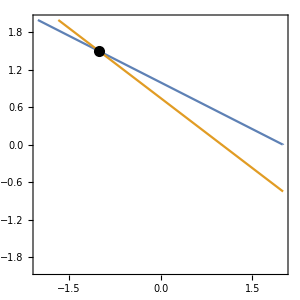

```mathematica
ContourPlot[{1r+2s==2,3r+4s==3},{r,-2,2},{s,-2,2},]
```

## Matrix Equation ↔ System of Equations

Begin with a set of equations:

```mathematica
equations={1r+2s==2,3r+4s==3};
```

This list of equations can be rewritten as a matrix equation as follows:

```mathematica
A={{1,2},{3,4}};
```

Define the vector of variables x and the nonhomogeneous vector b:

```mathematica
x={r,s};
b={2,3};
```

Thus, the matrix equation becomes:

```mathematica
A.x==b
```

{r+2 s,3 r+4 s}=={2,3}

## Solve Systems of Equations and Matrix Equations

Solve the system of equations:

```mathematica
equations={1r+2s==2,3r+4s==3};
Solve[equations]
```

{{r→-1,s→3/2}}

Solve the equivalent matrix equation with LinearSolve:

```mathematica
A={{1,2},{3,4}};
b={2,3};
LinearSolve[A,b]
```

{-1,3/2}

## If A is Invertible

When the matrix A is invertible, then there is a unique x that solves this equation.

This can be found by multiplying both sides of the equation by A^-1:

A x = b → x = A^-1 b

```mathematica
A={{1,2},{3,4}};
b={2,3};
Inverse[A].b
```

{-1,3/2}

This confirms the previous result.

## Homogeneous vs. Nonhomogeneous

The equation A.x=b with b=0 is said to be homogeneous.

When b≠0, the equation is nonhomogeneous.

When A is invertible, the only solution to the homogeneous equation A.x=0 is the solution x=0:

```mathematica
A={{1,2},{3,4}};
b={0,0};
Inverse[A].b
```

{0,0}

## If A is Noninvertible

When the matrix A is not invertible, then there is either no solution or there are infinitely many solutions:

```mathematica
A={{1,2},{3,6}};
A//MatrixForm
Inverse[A]
```

(1 | 2
3 | 6)

Inverse::sing: Matrix {{1,2},{3,6}} is singular.

Inverse[{{1,2},{3,6}}]

In such a case, Solve will give the solution for one variable in terms of the other:

```mathematica
Solve[A.x=={0,0},x]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s→-r/2}}

This demonstrates the fact that there are infinitely many solutions to this matrix equation.

## If A is Noninvertible

The nonhomogeneous equation A.x=b is more difficult to characterize.

Consider the equation A.x=b where A is not invertible and b is not zero.

If, for all vectors y satisfying A^*y=0, it is true that b^T y = 0, the equation A.x =b has infinitely many solutions.

If, for some vector y satisfying A^*y=0, it is not true that b^T y = 0, the equation A.x=b has no solution.

## Row Reduction

These previously mentioned results are important, but it is generally best to use row reduction to transform the system into a much simpler one.

After this step is performed, discovering solutions becomes much easier.

Suppose it is necessary to find solutions to the equation A.x=b where A =(1 | 2
3 | 6) and b = (2
3):

```mathematica
A={{1,2},{3,6}};
b={2,3};
```

Create an augmented matrix with the command:

```mathematica
(Ab={{1,2,2},{3,6,3}})//MatrixForm
```

(1 | 2 | 2
3 | 6 | 3)

Using this, reduce the augmented matrix to be a more simplified form:

```mathematica
RowReduce[Ab]//MatrixForm
```

(1 | 2 | 0
0 | 0 | 1)

## Row Reduction

Recalling that this matrix is actually equivalent to the system of equations, extract the information necessary:

```mathematica
RowReduce[Ab]//MatrixForm
```

(1 | 2 | 0
0 | 0 | 1)

The first line states that

1 x_1+2 x_2=0

and the second line reveals that

0 x_1+0 x_2=1.

This is an impossible equality, as there are no values of x_1 and x_2 such that 0 x_1+0 x_2=1.

Thus, there can be no solution that can solve this system of equations.

## Example 1

Solve the system of equations:

α-2β+3γ=7
-α+β-3γ=6
2α-β-γ=4

Construct the matrix equation A.x=b for this system of equations.

The matrix A is constructed as the coefficients of each term of the equation:

```mathematica
A={{1,-2,3},{-1,1,-3},{2,-1,-1}};
```

The vector b is the vector that appears on the right-hand side of the equations:

```mathematica
b={7,6,4};
```

## Example 1

With these two objects defined, the next step is searching for a vector x=(α
β
γ) that solves this equation.

Check first whether A is invertible:

```mathematica
Inverse[A]
```

{{-4/7,-5/7,3/7},{-1,-1,0},{-1/7,-3/7,-1/7}}

Because A is invertible, the solution is x=A^-1 b:

```mathematica
Inverse[A].b
```

{-46/7,-13,-29/7}

This can be confirmed using Solve:

```mathematica
Solve[{α-2β+3 γ==7,-α+β-3γ==6,2α-β-γ==4},{α,β,γ}]
```

{{α→-46/7,β→-13,γ→-29/7}}

## Example 2

Solve the system of equations:

α+4β+3γ=7
3α+β-2γ=6
2α+β-γ=4

The matrix A is constructed as the coefficients of each term of the equation:

```mathematica
A={{1,4,3},{3,1,-2},{2,1,-1}};
```

The vector b is the vector that appears on the right-hand side of the equations:

```mathematica
b={7,6,4};
```

## Example 2

With these two objects defined, the next step is searching for a vector x=(α
β
γ) that solves this equation.

There many ways to go about this. It is best to check first whether A is invertible:

```mathematica
Inverse[A]
```

Inverse::sing: Matrix {{1,4,3},{3,1,-2},{2,1,-1}} is singular.

Inverse[{{1,4,3},{3,1,-2},{2,1,-1}}]

Because A is not invertible, row reduction must be used:

```mathematica
RowReduce[{{1,4,3,7},{3,1,-2,6},{2,1,-1,4}}]//MatrixForm
```

(1 | 0 | -1 | 0
0 | 1 | 1 | 0
0 | 0 | 0 | 1)

Since the last row implies the equation 0α+0β+0γ=1, which is impossible, you can conclude that there are no solutions to this system of equations.

## Summary

Using the theorems of linear algebra will be critical to solving systems of differential equations.

It was found that solving systems of equations can be reduced to a much simpler form through the use of matrix equations.

It will later be demonstrated that this is also true for systems of differential equations.